```mathematica
(5*^-3*0.2*^-3)/(π 7.8*10^-7)
```

0.40809

```mathematica
"magnification"
(110*3.45)/125
"microns (object space) per pixel"
125/110//N
```

magnification

3.036

microns (object space) per pixel

1.13636

```mathematica
"magnification"
m=28.57;(*(110*3.45)/125*)
"microns (object space) per pixel"
perpix=1/m 3.45//N
```

magnification

microns (object space) per pixel

0.120756

```mathematica
perpix*1080
```

130.417

```mathematica
124.2
```

124.2

```mathematica
2/perpix
```

17.3913

```mathematica
Clear[o];
f=8;
(*o=(1/f-1/i)^-1;*)
m=-31.15;
NSolve[{m==(-i)/o,1/o==1/f-1/i},{i,o}]
```

{{i→257.2,o→8.25682}}

```mathematica
Plot[-i/o,{i,125,150}]
Plot[o,{i,125,135}]
```

-Graphics-

```mathematica
0.6/perpix
```

4.9687

```mathematica
λ
```

7.8×10^-7

Imaging the parabolic mirror focus on the Thorlabs camera. Seeing how grainy the beam will appear.

magnification

23.4375

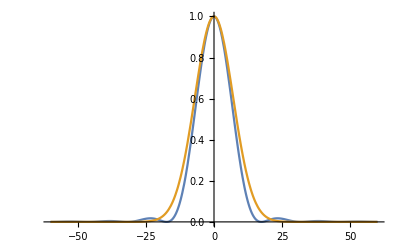

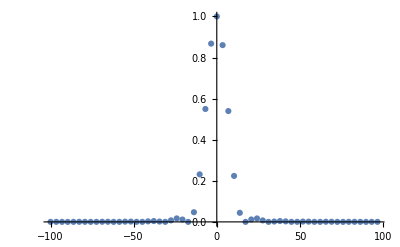

-Graphics-

```mathematica
pixsize=3.45;(*micron*)
xmax=100; (*the image space ROI in um, i.e. the actual distance on the camera array*)
xpts=Range[-xmax,xmax,pixsize];
k=2π/λ;
a=0.0205;(*the limiting aperture*)
f1=0.032;
f2=0.75;(*the last lens before the camera*)
"magnification"
M=f2/f1
w0=0.6;(*focal spot in micron. this is what we're imaging*)
w=M*w0;(*focal spot size on the camera. um*)
AiryDisk[ρ_,f_]:=((2BesselJ[1,(a k)/f ρ])/((a k)/f ρ))^2;
Plot[{AiryDisk[x*10^-6,f2],Exp[-2(x/w)^2]},{x,-60,60},PlotRange->All]
ListPlot[Table[{x,AiryDisk[10^-6 x,f2]},{x,xpts}],PlotRange->All]
Show[Table[Image[Table[Exp[-2((√(x^2+y^2))/(w0 f/f1))^2],{x,xpts},{y,xpts}]],{f,{0.5,0.75,1}}],ImageSize->Medium,Framed->{True,True},FrameLabel->{"micron","micron"}]
```

```mathematica
AiryDisk[√(x^2+y^2),f]
```

(1.46684×10^-10 f^2 BesselJ[1,(165135. √(x^2+y^2))/f]^2)/(x^2+y^2)

```mathematica
Table[Colorize[Image[Table[AiryDisk[10^-6 √(x^2+y^2),f],{x,xpts},{y,xpts}],ImageSize->Small],ColorFunction->"ThermometerColors"],{f,{0.5,0.75,1,1.5}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Image[Table[Exp[-2((√(x^2+y^2))/(w0 f/f1))^2],{x,xpts},{y,xpts}],ImageSize->Small],{f,{0.5,0.75,1,1.5}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

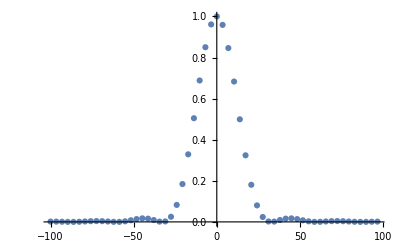

-Graphics-

x = πq/λN, where λ is the wavelength of the light, q is the radical distance from the optical axis, and N = R/d with d = 2a and R the observation distance

```mathematica
perpix
```

0.120756

```mathematica
Table[(BesselJ[1, α w √(x^2+y^2)]/(α w √(x^2+y^2)))^2,{x,xpts},{y,xpts}]//Dimensions
```

{17,17}

```mathematica
Table[{x,y,3.9(BesselJ[1, α w √(x^2+y^2)]/(α w √(x^2+y^2)))^2},{x,xpts},{y,xpts}][[1]]
```

{{-1.,-1.,0.00917608},{-1.,-0.885,0.0137961},{-1.,-0.77,0.0166132},{-1.,-0.655,0.0168312},{-1.,-0.54,0.0147569},{-1.,-0.425,0.0114806},{-1.,-0.31,0.00822544},{-1.,-0.195,0.00580834},{-1.,-0.08,0.00450723},{-1.,0.035,0.004299},{-1.,0.15,0.00516466},{-1.,0.265,0.00715382},{-1.,0.38,0.0101466},{-1.,0.495,0.0135462},{-1.,0.61,0.0162433},{-1.,0.725,0.0170147},{-1.,0.84,0.0151813},{-1.,0.955,0.0111061}}

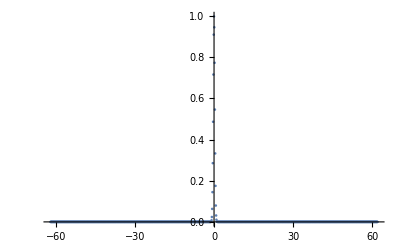

```mathematica
ListPlot[{Table[{x,Exp[-2(x/w)^2]},{x,xpts}]},PlotLegends->"Expressions",PlotRange->All]
```

```mathematica
ListContourPlot
```

Two lens imaging.

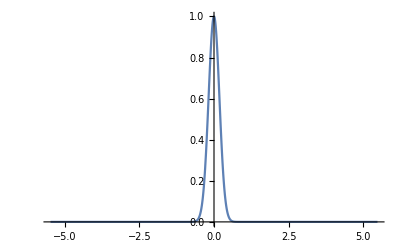

```mathematica
Plot[Exp[-2(x/(.363))^2],{x,-5.485,5.485},PlotRange->All]
```

Image size vs lens foci misalignment

```mathematica
MLens[f_]:={{1,0},{-1/f,1}};
Md[d_]:={{1,d},{0,1}};
f1=32;
f2=996;
Mtotal=Md[f2+10].MLens[f2].Md[10].MLens[f1].Md[f1+100];
X={0.125,0};
X2=Mtotal.X
"Magnification"
X2[[1]]/X[[1]]
```

{-3.93055,-0.00399253}

Magnification

-31.4444

{-3.93055,-0.00399253}

-31.4444

```mathematica
NSolve[(Md[d].MLens[f2].Md[10].MLens[f1].Md[f1].X)[[2]]==0,d]
```

{}

```mathematica
(Md[d].MLens[f2].Md[10].MLens[f1].Md[f1].X)
```

{0.125 (1+1/32 (-10 (1-d/996)-d)-d/996),-0.00399253}

```mathematica
Md[d]
```

{{1,d},{0,1}}